## 5-band Model

Based on Appendix D: https://arxiv.org/abs/1808.02482

### Initialization cells

lattice vectors

```mathematica
a:={1/2{√3,-1},{0,1}}
```

k vector

```mathematica
k:={kx,ky}
```

phi function

```mathematica
phi[l_,m_]:=Exp[-ⅈ k.(l a[[1]]+m a[[2]])]
```

wavefunction parameters

```mathematica
at=0.25;
bt=0.2;
ct=0.1;
dt=0.67;
```

Hamiltonian parameters (in units of meV)

```mathematica
t0=1;
mupz=-0.043 t0;
muppm=0 t0;
munu=0.05 t0;
```

phase factors

```mathematica
zeta=Exp[ⅈ (2π)/6];
omega=Exp[ⅈ (2π)/3];
```

### Constructing the Hamiltonian

rho matrix (equation D2)

```mathematica
rho1={ⅈ at(phi[1,1]-phi[1,0]),
	bt phi[1,1]+ct phi[1,0], 
	ct phi[1,1]+bt phi[1,0],
	Conjugate[dt] phi[1,0],
	dt};
rho2={ⅈ at (1-phi[1,1]), 
         omega(bt+ct phi[1,1]), 
	Conjugate[omega](ct+bt phi[1,1]), 
	Conjugate[dt], 
	dt};
rho3={ⅈ at (phi[1,0]-1), 
	Conjugate[omega](bt phi[1,0]+ct), 
	omega(ct phi[1,0]+bt), 
	Conjugate[dt]phi[0,1],
	dt};
rho=Transpose[{rho1,rho2,rho3}];
```

Hamiltonian (equation D3)

```mathematica
Hraw=-t0 rho.FullSimplify[ConjugateTranspose[rho],Assumptions->{kx∈Reals,ky∈Reals}] + DiagonalMatrix[{mupz,muppm,muppm,munu,munu}];
H=Chop[FullSimplify[Hraw]];
```

### Band structure

#### Investigate where the high-symmetry points are

```mathematica
h1raw=Eigenvalues[H][[1]];
```

```mathematica
h1=Chop[FullSimplify[h1raw,Assumptions->{kx∈Reals,ky∈Reals}]];
```

```mathematica
h1slice=h1/.ky->-√3 kx;
```

```mathematica
Show[Plot3D[h1,{kx,-π,π},{ky,-π,π}, AxesLabel->{"kx","ky","E"}, BoxRatios->Automatic,PlotStyle->Opacity[0.3]],Graphics3D[{Red,PointSize[0.1],Point[{0,0,0}],Point[{(-2π)/(3 √3),(+2π)/3,0}]}]]
```

-Graphics3D-

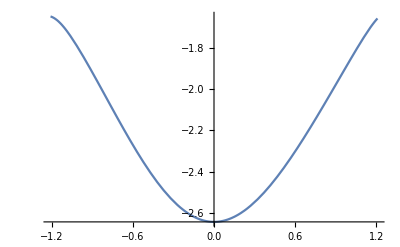

```mathematica
Plot[h1slice,{kx,(-2π)/(3 √3),(2π)/(3 √3)}]
```

#### Naive 3D plot of band structure

```mathematica
h1raw=Eigenvalues[H][[1]];
h2raw=Eigenvalues[H][[2]];
h3raw=Eigenvalues[H][[3]];
h4raw=Eigenvalues[H][[4]];
h5raw=Eigenvalues[H][[5]];
```

```mathematica
h1=Chop[FullSimplify[h1raw,Assumptions->{kx∈Reals,ky∈Reals}]];
h2=Chop[FullSimplify[h2raw,Assumptions->{kx∈Reals,ky∈Reals}]];
h3=Chop[FullSimplify[h3raw,Assumptions->{kx∈Reals,ky∈Reals}]];
h4=Chop[FullSimplify[h4raw,Assumptions->{kx∈Reals,ky∈Reals}]];
h5=Chop[FullSimplify[h5raw,Assumptions->{kx∈Reals,ky∈Reals}]];
```

```mathematica
Plot3D[{h1,h2,h3,h4,h5},{kx,-π,π},{ky,-π,π}, AxesLabel->{"kx","ky","E"}, BoxRatios->Automatic]
```

-Graphics3D-

#### 2D Plot along the K->-K high-symmetry line

```mathematica
h1slice=h1/.ky->-√3 kx;
h2slice=h2/.ky->-√3 kx;
h3slice=h3/.ky->-√3 kx;
h4slice=h4/.ky->-√3 kx;
h5slice=h5/.ky->-√3 kx;
```

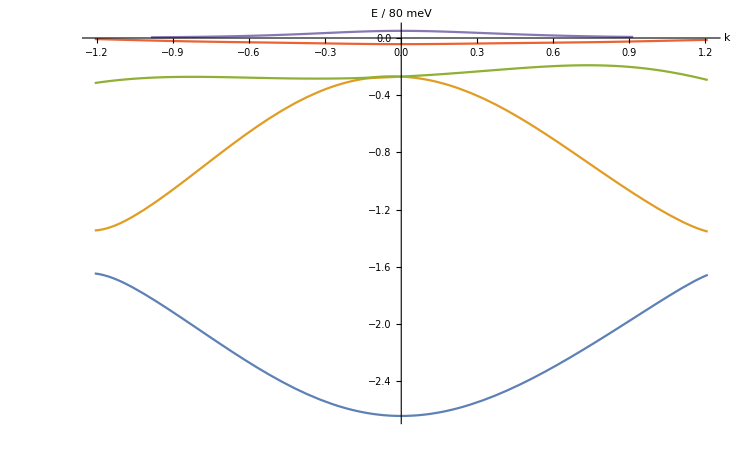

```mathematica
Plot[{h1slice,h2slice,h3slice,h4slice,h5slice},{kx,(-2π)/(3 √3),(2π)/(3 √3)},AxesLabel->{"k","E / 80 meV"}]
```

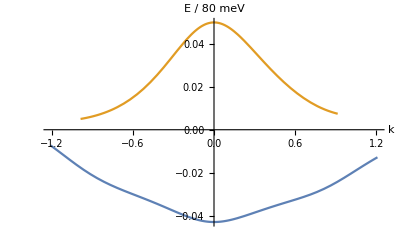

```mathematica
Plot[{h4slice,h5slice},{kx,(-2π)/(3 √3),(2π)/(3 √3)},AxesLabel->{"k","E / 80 meV"}]
```

### Hexagonal Lattice

```mathematica
NN={1/2{√3,1},{0,1},-1/2{√3,1},-{0,1},1/2{√3,-1},1/2{-√3,1}};
nNN={{√3,0},{-√3,0},1/2{√3,3},-1/2{√3,3},1/2{-√3,3},1/2{√3,-3}};
nnNN={{0,2},{0,-2},{√3,1},-{√3,1},{-√3,1},{√3,-1}};
```

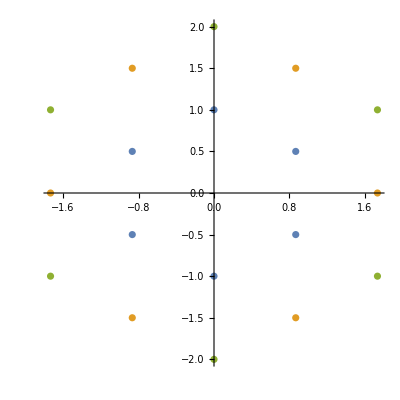

```mathematica
ListPlot[{NN,nNN,nnNN},AspectRatio->1]
```